```mathematica
skip=20;
du=dv=1/100;
massReduct=1/500;
v1= 0;
m0=1;
Q0=8/10;
SourcesRParam = 1;
SourcesRParamR =1;
SourcesSParam = 1;
SourcesSParamR =1;
SourcesS5Param =0;
deltaUV5Param = 70;
QuvFactor =1;
Qreduct=Q0/m0*massReduct;
deltav =400;
v2 =v1+deltav;
RStarConst =-30;
Vvec = Table[v,{v,v1,v2,dv}];
MFunc = (m0^3-(v-v1)*massReduct)^(1/3);
QFunc = MFunc * Q0;
Clear[pdesolskip,RTable,STable,RvTable,RvvTable,RuTable,RuuTable,SvTable,SvvTable,SuTable,SuuTable];
Uvec = 2*RStarConst- Vvec;
Uvec0=Table[u,{u,Uvec[[-1]],Uvec[[1]],du}];
UvecSkipped = Uvec0[[1;;-1;;skip]];
VvecSkipped = Vvec[[1;;-1;;skip]];
deltaUV5 = (Uvec0[[1]]+Vvec[[1]])/2+deltaUV5Param; 
vsol=DSolve[{H'[v]==κp/.{Q->QFunc,m->MFunc},H[0]==0},H[v],{v,v1,v2}(*,Method->"StiffnessSwitching",WorkingPrecision->60*)];
vtilde=(H[v]/.vsol/.{v->Vvec})[[1]];
usol=DSolve[{H'[u]==κp/.{Q->(QFunc/.v->-u),m->(MFunc/.v->-u)},H[0]==0},H[u],u(*,{u,Uvec[[1]],Uvec[[-1]]},Method->"StiffnessSwitching",WorkingPrecision->60*)];
utilde=(H[u]/.usol/.{u->Uvec})[[1]];
Ttilde=(utilde+vtilde)/2;
MTable= MFunc/.{v->Vvec}//N100;
QTable = QFunc/.{v->Vvec}//N100;
QuvTable = QuvFactor *massReduct* MTable^-1 ;
QuvScale=MTable^-1;
MuTable = MFunc /. {v->-Uvec}//N100;
QuTable = QFunc /. {v->-Uvec}//N100;
κpu=(κp/.{m->μ,Q->Qu});
sInitFixed = Log[-r *f/2]+Log[κpu]-Log[κp];
DRDUFixed=r f *κpu/κp;
DLogκpuDu=D[Log[κpu],μ]*D[(MFunc/.v->-u),u]+D[Log[κpu],Qu]*D[(QFunc/.v->-u),u];
DSDUFixed=D[Log[-r f ],r] *DRDUFixed/(2r)+DLogκpuDu;
SourcesR=massReduct*SourcesRParam/MTable^3;
SourcesS = massReduct*SourcesSParam/MTable^5;
SourcesRR =massReduct* SourcesRParamR/MTable^4;
SourcesRS = massReduct*SourcesSParamR/MTable^6;
SourcesR5=0*Vvec;
SourcesS5 = massReduct*SourcesS5Param*MTable;
time0=AbsoluteTiming[
RStarVector=Table[ (Ttilde[[j]]/κp/.{m->MTable[[j]],Q->QTable[[j]]}),{j,1,Length[MTable]}];
rInit=Table[RFromRStar[RStarVector[[j]],MTable[[j]],QTable[[j]]],{j,1,Length[MTable]}];
RInitVector = Table[ rInit[[j]]^2,{j,1,Length[MTable]}];
SInitVector =  Table[ (sInitFixed/.{m->MTable[[j]],μ->MuTable[[j]],r->rInit[[j]],Q->QTable[[j]],Qu->QuTable[[j]]})//N,{j,1,Length[MTable]}];
DRInitVector =  Table[ (DRDUFixed/.{m->MTable[[j]],μ->MuTable[[j]],r->rInit[[j]],Q->QTable[[j]],Qu->QuTable[[j]]})//N,{j,1,Length[MTable]}];
DSInitVector =  Table[ (DSDUFixed/.{m->MTable[[j]],μ->MuTable[[j]],u->Uvec[[j]],r->rInit[[j]],Q->QTable[[j]],Qu->QuTable[[j]]})//N,{j,1,Length[MTable]}];
midpointDR = (DRInitVector[[2;;]]+DRInitVector[[;;-2]])/2;
midpointDS = (DSInitVector[[2;;]]+DSInitVector[[;;-2]])/2;
{Ruv,Suv}=ComputeRuvSuvQuvScale[RInitVector,SInitVector,(QTable[[2;;]]+QTable[[;;-2]])/2,SourcesR,SourcesS,QuvTable,Uvec0[[1]]+Vvec[[1]],QuvScale, dv,SourcesRR,SourcesRS,SourcesR5,SourcesS5,deltaUV5];
R2InitVector=RInitVector[[2;;]]+du*(midpointDR+1/2*dv*Ruv);
S2InitVector=SInitVector[[2;;]]+du*(midpointDS+1/2*dv*Suv);]
time2=AbsoluteTiming[pdesolskip=pyPdeSolveQuvScale[skip,R2InitVector,RInitVector,S2InitVector,SInitVector,(QTable//N),(du//N),(dv//N),SourcesR//N,SourcesS//N,QuvTable//N,(Uvec0[[1]]+Vvec[[1]])//N, QuvScale // N,SourcesRR//N,SourcesRS//N,SourcesR5 // N,SourcesS5//N,deltaUV5//N];]
(* R,S,Rv,Rvv,Ru,Ruu,Sv,Svv,Su,Suu *)
RTable = Normal[pdesolskip[[1]]];
STable = Normal[pdesolskip[[2]]];
RvTable = Normal[pdesolskip[[3]]];
RvvTable = Normal[pdesolskip[[4]]];
RuTable = Normal[pdesolskip[[5]]];
RuuTable = Normal[pdesolskip[[6]]];
SvTable = Normal[pdesolskip[[7]]];
SvvTable = Normal[pdesolskip[[8]]];
SuTable = Normal[pdesolskip[[9]]];
SuuTable = Normal[pdesolskip[[10]]];
RTables[du]=RTable;
STables[du]=STable;
cu = RuTable*SuTable-RuuTable;
cv = RvTable*SvTable-RvvTable;
cuv = cu-cv;
```

{44.4311,Null}

10% Done

20% Done

30% Done

40% Done

50% Done

60% Done

70% Done

80% Done

90% Done

100% Done

Done calculating

{32.9588,Null}

```mathematica
RTables[massReduct] = RTable;
STables[massReduct] = STable;
RvTables[massReduct] = RvTable;
RvvTables[massReduct] = RvvTable;
RuTables[massReduct] = RuTable;
RuuTables[massReduct] = RuuTable;
SvTables[massReduct] = SvTable;
SvvTables[massReduct] = SvvTable;
SuTables[massReduct] = SuTable;
SuuTables[massReduct] = SuuTable;
cus[massReduct]=cu;
cvs[massReduct]=cv;
MTables[massReduct] = MTable;
QTables[massReduct] = QTable;
MFuncs[massReduct]=MFunc;
QFuncs[massReduct]=QFunc;
UvecSkippeds[massReduct]=UvecSkipped;
```

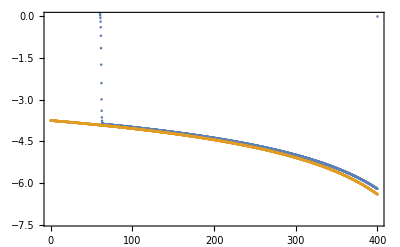

```mathematica
ListPlot[{{VvecSkipped,SvTable[[;;,-1]]}//Transpose,{VvecSkipped,-κm/.{m->MTable[[1;;-1;;skip]],Q->QTable[[1;;-1;;skip]]}}//Transpose},Frame->True,FrameLabel->{MaTeX@"v"},PlotLegends->MaTeX/@{"S_{,v}","-\\kappa_-^v"}]
```

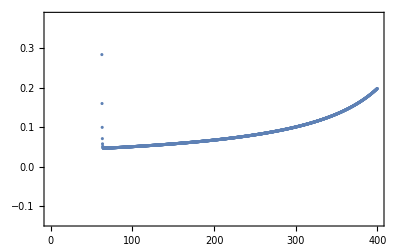

```mathematica
κmVec = -κm/.{m->MTable[[1;;-1;;skip]],Q->QTable[[1;;-1;;skip]]};
ListPlot[{VvecSkipped,SvTable[[;;,-1]]-κmVec}//Transpose,Frame->True,FrameLabel->{MaTeX@"v",Rotate[MaTeX@"S_{,v}+\\kappa_-^v",-90 Degree]}]
```

```mathematica
κmVec = -κm/.{m->MTable[[1;;-1;;skip]],Q->QTable[[1;;-1;;skip]]};
```

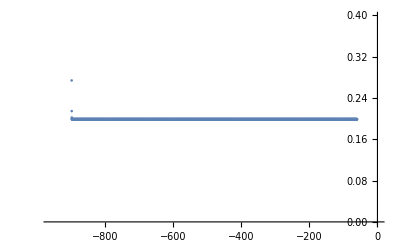

```mathematica
ListPlot[{UvecSkipped,SvTable[[-3,;;]]-κmVec[[-3]]}//Transpose]
```

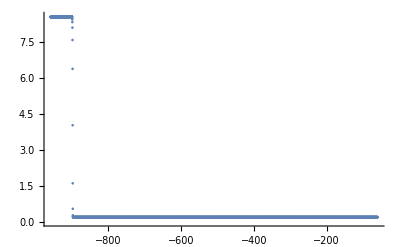

```mathematica
ListPlot[{UvecSkipped[[4;;]],SvTable[[-3,4;;]]-κmVec[[-3]]}//Transpose,PlotRange->All]
```

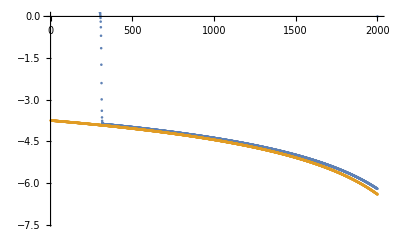

```mathematica
ListPlot[{SvTables[1/500][[;;,-1]],-κm/.{m->MTables[1/500][[1;;-1;;skip]],Q->QTables[1/500][[1;;-1;;skip]]}}]
```

```mathematica
TheImageSize=300;
```

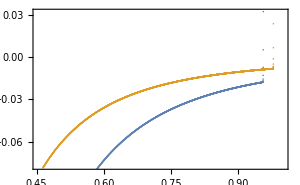

```mathematica
κmVecs[1/1000]=-κm/.{m->MTables[1/1000][[1;;-1;;skip]],Q->QTables[1/1000][[1;;-1;;skip]]};
κmVecs[1/500]=-κm/.{m->MTables[1/500][[1;;-1;;skip]],Q->QTables[1/500][[1;;-1;;skip]]};
ExportAndShow["S,v+κm ε comparison",ListPlot[{{MTables[1/500][[1;;-1;;skip]],SvTables[1/500][[;;,-1]]-κmVecs[1/500]}//Transpose,{MTables[1/1000][[1;;-1;;skip]],SvTables[1/1000][[;;,-1]]-κmVecs[1/1000]}//Transpose},Frame->True,FrameLabel->{MaTeX@"M",Rotate[MaTeX@"S_{,v}+\\kappa_-^v",-90 Degree]},PlotLegends->{MaTeX@"\\varepsilon_0=\\frac{1}{500}",MaTeX@"\\varepsilon_0=\\frac{1}{1000}"},ImageSize->TheImageSize]]
```

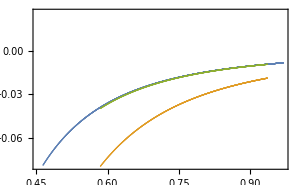

```mathematica
startj=450;
κmVecs[1/1000]=-κm/.{m->MTables[1/1000][[1;;-1;;skip]],Q->QTables[1/1000][[1;;-1;;skip]]};
κmVecs[1/500]=-κm/.{m->MTables[1/500][[1;;-1;;skip]],Q->QTables[1/500][[1;;-1;;skip]]};
ExportAndShow["S,v+κm ε 2x comparison",ListPlot[{({MTables[1/1000][[1;;-1;;skip]],SvTables[1/1000][[;;,-1]]-κmVecs[1/1000]}//Transpose)[[startj;;]],({MTables[1/500][[1;;-1;;skip]],(SvTables[1/500][[;;,-1]]-κmVecs[1/500])}//Transpose)[[startj;;]],
({MTables[1/500][[1;;-1;;skip]],(SvTables[1/500][[;;,-1]]-κmVecs[1/500])/2}//Transpose)[[startj;;]]},Frame->True,FrameLabel->{MaTeX@"M",Rotate[MaTeX@"S_{,v}+\\kappa_-^v",-90 Degree]},PlotLegends->Placed[{MaTeX@"\\varepsilon_0=\\frac{1}{1000}",MaTeX@"\\varepsilon_0=\\frac{1}{500}",MaTeX@"\\varepsilon_0=\\frac{1}{500},\\;\\left(\\times\\frac{1}{2}\\right)"},Right],ImageSize->TheImageSize]]
```

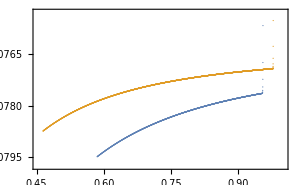

```mathematica
κmVecs[1/1000]=-κm/.{m->MTables[1/1000][[1;;-1;;skip]],Q->QTables[1/1000][[1;;-1;;skip]]};
κmVecs[1/500]=-κm/.{m->MTables[1/500][[1;;-1;;skip]],Q->QTables[1/500][[1;;-1;;skip]]};
ExportAndShow["S,v+κm ε 2x scaling",ListPlot[{{MTables[1/500][[1;;-1;;skip]],MTables[1/500][[1;;-1;;skip]]^3*(SvTables[1/500][[;;,-1]]-κmVecs[1/500])/2}//Transpose,{MTables[1/1000][[1;;-1;;skip]],MTables[1/1000][[1;;-1;;skip]]^3*(SvTables[1/1000][[;;,-1]]-κmVecs[1/1000])}//Transpose},Frame->True,FrameLabel->{MaTeX@"M",Rotate[MaTeX@"\\left(S_{,v}+\\kappa_{-}\\right)M^{3}",-90 Degree]},PlotLegends->Placed[{MaTeX@"\\varepsilon_0=\\frac{1}{500},\\;\\left(\\times\\frac{1}{2}\\right)",MaTeX@"\\varepsilon_0=\\frac{1}{1000}"},Right],ImageSize->TheImageSize]]
```

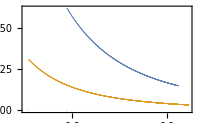

```mathematica
TvvApproxVecs[1/1000]=(-cvs[1/1000][[;;,-1]]/(κm/.{m->MTables[1/1000][[1;;-1;;skip]],Q->QTables[1/1000][[1;;-1;;skip]]}))[[450;;]];
TvvApproxVecs[1/500]=(-cvs[1/500][[;;,-1]]/(κm/.{m->MTables[1/500][[1;;-1;;skip]],Q->QTables[1/500][[1;;-1;;skip]]}))[[450;;]];
ExportAndShow["R,v-approx ε comparison",ListPlot[{{MTables[1/500][[449*skip+1;;-1;;skip]],(RvTables[1/500][[450;;,-1]]-TvvApproxVecs[1/500])}//Transpose,{MTables[1/1000][[449*skip+1;;-1;;skip]],RvTables[1/1000][[450;;,-1]]-TvvApproxVecs[1/1000]}//Transpose},Frame->True,FrameLabel->{MaTeX@"M",Rotate[MaTeX@"R_{,v}+\\frac{\\widetilde{T}_{vv}}{\\kappa_{-}^{v}}",-90 Degree]},PlotLegends->{MaTeX@"\\varepsilon_0=\\frac{1}{500}",MaTeX@"\\varepsilon_0=\\frac{1}{1000}"},ImageSize->TheImageSize]]
```

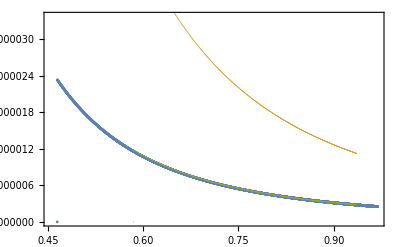

```mathematica
TvvApproxVecs[1/1000]=(-cvs[1/1000][[;;,-1]]/(κm/.{m->MTables[1/1000][[1;;-1;;skip]],Q->QTables[1/1000][[1;;-1;;skip]]}))[[450;;]];
TvvApproxVecs[1/500]=(-cvs[1/500][[;;,-1]]/(κm/.{m->MTables[1/500][[1;;-1;;skip]],Q->QTables[1/500][[1;;-1;;skip]]}))[[450;;]];
ExportAndShow["R,v-approx ε x4 comparison",ListPlot[{{MTables[1/1000][[449*skip+1;;-1;;skip]],RvTables[1/1000][[450;;,-1]]-TvvApproxVecs[1/1000]}//Transpose,{MTables[1/500][[449*skip+1;;-1;;skip]],(RvTables[1/500][[450;;,-1]]-TvvApproxVecs[1/500])}//Transpose,
{MTables[1/500][[449*skip+1;;-1;;skip]],(RvTables[1/500][[450;;,-1]]-TvvApproxVecs[1/500])/4}//Transpose},Frame->True,FrameLabel->{MaTeX@"M",Rotate[MaTeX@"R_{,v}+\\frac{\\widetilde{T}_{vv}}{\\kappa_{-}^{v}}",-90 Degree]},PlotLegends->{MaTeX@"\\varepsilon_0=\\frac{1}{1000}",MaTeX@"\\varepsilon_0=\\frac{1}{500}",MaTeX@"\\varepsilon_0=\\frac{1}{500}\\;\\left(\\times\\frac{1}{4}\\right)"},PlotStyle->{PointSize[0.005],PointSize[0.0001],PointSize[0.0001]}]]
```

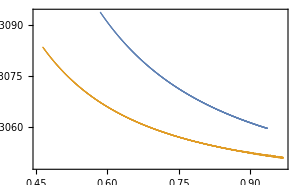

```mathematica
TvvApproxVecs[1/1000]=(-cvs[1/1000][[;;,-1]]/(κm/.{m->MTables[1/1000][[1;;-1;;skip]],Q->QTables[1/1000][[1;;-1;;skip]]}))[[450;;-2]];
TvvApproxVecs[1/500]=(-cvs[1/500][[;;,-1]]/(κm/.{m->MTables[1/500][[1;;-1;;skip]],Q->QTables[1/500][[1;;-1;;skip]]}))[[450;;-2]];
ExportAndShow["R,v-approx ε x4 scaling",ListPlot[{{MTables[1/500][[449*skip+1;;-1-skip;;skip]],MTables[1/500][[449*skip+1;;-1-skip;;skip]]^3*(RvTables[1/500][[450;;-2,-1]]-TvvApproxVecs[1/500])/4}//Transpose,{MTables[1/1000][[449*skip+1;;-1-skip;;skip]],MTables[1/1000][[449*skip+1;;-1-skip;;skip]]^3*(RvTables[1/1000][[450;;-2,-1]]-TvvApproxVecs[1/1000])}//Transpose},Frame->True,FrameLabel->{MaTeX@"M",Rotate[MaTeX@"\\left(R_{,v}+\\frac{\\widetilde{T}_{vv}}{\\kappa_{-}}\\right)M^{3}",-90 Degree]},PlotLegends->{MaTeX@"\\varepsilon_0=\\frac{1}{500}\\;\\left(\\times\\frac{1}{4}\\right)",MaTeX@"\\varepsilon_0=\\frac{1}{1000}"},ImageSize->300]]
```

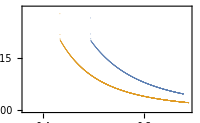

```mathematica
κmVecs[1/1000]=(-κm/.{m->MFuncs[1/1000],Q->QFuncs[1/1000]})/.{v->-UvecSkippeds[1/1000]};
κmVecs[1/500]=(-κm/.{m->MFuncs[1/500],Q->QFuncs[1/500]})/.{v->-UvecSkippeds[1/500]};
ExportAndShow["S,u+κm ε comparison",ListPlot[{{MFuncs[1/500]/.{v->-UvecSkippeds[1/500]},SuTables[1/500][[-1,;;]]-κmVecs[1/500]}//Transpose,{MFuncs[1/1000]/.{v->-UvecSkippeds[1/1000]},SuTables[1/1000][[-1,;;]]-κmVecs[1/1000]}//Transpose},Frame->True,FrameLabel->{MaTeX@"M^u",Rotate[MaTeX@"S_{,u}+\\kappa_-^u",-90 Degree]},PlotLegends->{MaTeX@"\\varepsilon_0=\\frac{1}{500}",MaTeX@"\\varepsilon_0=\\frac{1}{1000}"},ImageSize->TheImageSize]]
```

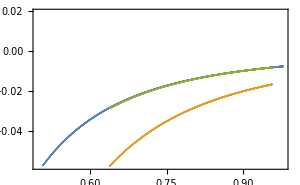

```mathematica
κmVecs[1/1000]=(-κm/.{m->MFuncs[1/1000],Q->QFuncs[1/1000]})/.{v->-UvecSkippeds[1/1000]};
κmVecs[1/500]=(-κm/.{m->MFuncs[1/500],Q->QFuncs[1/500]})/.{v->-UvecSkippeds[1/500]};
startj=450;
ExportAndShow["S,u+κm ε 2x comparison",ListPlot[{({MFuncs[1/1000]/.{v->-UvecSkippeds[1/1000]},SuTables[1/1000][[-1,;;]]-κmVecs[1/1000]}//Transpose)[[startj;;]],({MFuncs[1/500]/.{v->-UvecSkippeds[1/500]},(SuTables[1/500][[-1,;;]]-κmVecs[1/500])}//Transpose)[[startj;;]],({MFuncs[1/500]/.{v->-UvecSkippeds[1/500]},(SuTables[1/500][[-1,;;]]-κmVecs[1/500])/2}//Transpose)[[startj;;]]},Frame->True,FrameLabel->{MaTeX@"M^u",Rotate[MaTeX@"S_{,u}+\\kappa_-^u",-90 Degree]},PlotLegends->{MaTeX@"\\varepsilon_0=\\frac{1}{1000}",MaTeX@"\\varepsilon_0=\\frac{1}{500}",MaTeX@"\\varepsilon_0=\\frac{1}{500}\\;\\left(\\times\\frac{1}{2}\\right)"},ImageSize->300]]
```

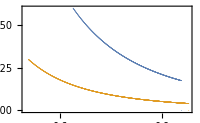

```mathematica
TvvApproxVecs[1/1000]=(-cus[1/1000][[-1,;;]]/((κm/.{m->MFuncs[1/1000],Q->QFuncs[1/1000]})/.{v->-UvecSkippeds[1/1000]}))[[450;;]];
TvvApproxVecs[1/500]=(-cus[1/500][[-1,;;]]/((κm/.{m->MFuncs[1/500],Q->QFuncs[1/500]})/.{v->-UvecSkippeds[1/500]}))[[450;;]];
ExportAndShow["R,u-approx ε comparison",ListPlot[{{(MFuncs[1/500]/.{v->-UvecSkippeds[1/500]})[[450;;]],(RuTables[1/500][[-1,450;;]]-TvvApproxVecs[1/500])}//Transpose,{(MFuncs[1/1000]/.{v->-UvecSkippeds[1/1000]})[[450;;]],(RuTables[1/1000][[-1,450;;]]-TvvApproxVecs[1/1000])}//Transpose},Frame->True,FrameLabel->{MaTeX@"M^u",Rotate[MaTeX@"R_{,u}+\\frac{\\widetilde{T}_{uu}}{\\kappa_{-}^{u}}",-90 Degree]},PlotLegends->{MaTeX@"\\varepsilon_0=\\frac{1}{500}",MaTeX@"\\varepsilon_0=\\frac{1}{1000}"},ImageSize->TheImageSize]]
```

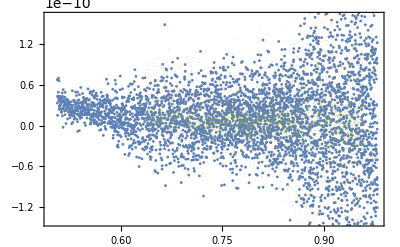

```mathematica
TvvApproxVecs[1/1000]=(-cus[1/1000][[-1,;;]]/((κm/.{m->MFuncs[1/1000],Q->QFuncs[1/1000]})/.{v->-UvecSkippeds[1/1000]}))[[450;;-2]];
TvvApproxVecs[1/500]=(-cus[1/500][[-1,;;]]/((κm/.{m->MFuncs[1/500],Q->QFuncs[1/500]})/.{v->-UvecSkippeds[1/500]}))[[450;;-2]];
ExportAndShow["R,u-approx ε x4 comparison",ListPlot[{{(MFuncs[1/1000]/.{v->-UvecSkippeds[1/1000]})[[450;;-2]],(RuTables[1/1000][[-1,450;;-2]]-TvvApproxVecs[1/1000])}//Transpose,{(MFuncs[1/500]/.{v->-UvecSkippeds[1/500]})[[450;;-2]],(RuTables[1/500][[-1,450;;-2]]-TvvApproxVecs[1/500])}//Transpose,{(MFuncs[1/500]/.{v->-UvecSkippeds[1/500]})[[450;;-2]],(RuTables[1/500][[-1,450;;-2]]-TvvApproxVecs[1/500])/4}//Transpose},Frame->True,FrameLabel->{MaTeX@"M^u",Rotate[MaTeX@"R_{,u}+\\frac{\\widetilde{T}_{uu}}{\\kappa_{-}^{u}}",-90 Degree]},PlotLegends->{MaTeX@"\\varepsilon_0=\\frac{1}{1000}",MaTeX@"\\varepsilon_0=\\frac{1}{500}",MaTeX@"\\varepsilon_0=\\frac{1}{500}\\;\\left(\\times\\frac{1}{4}\\right)"},PlotStyle->{PointSize[0.005],PointSize[0.0001],PointSize[0.0001]}]]
```